```mathematica
SetDirectory[NotebookDirectory[]];
```

# Model 019

## Constants

```mathematica
C1=303*10^-8;(*[Gyr]*)
C2=875*10^-7 ;(*[Gyr]*)
KK=810*10^-3 ;(*[Gyr (M_(\[PermutationProduct]))^(1/2) pc^(-3/2)]*)
P=404/10;  (*[(M_(\[PermutationProduct]))^-1 pc^3 cm^-3]*)
Rh=19/10;(*[cm^3 Gyr^-1]*)
σνB=8158;(*[cm^3 Gyr^-1]*)
Zsun=134/10000;
Zeff=10^-3*Zsun;
Zsn=9/100;
ηion=95529/100;
ηdiss=38093/100;
R=18/100;
```

## System of equations

```mathematica
(*
	Ionized gas fraction:        i(t) / ρ -> y[1]
	Atomic gas fraction:         a(t) / ρ -> y[2]
	Molecular gas fraction:      m(t) / ρ -> y[3]
	Metal fraction:              z(t) / ρ -> y[4]
	Stellar fraction:            s(t) / ρ -> y[5]	
	where ρ = i(t) + a(t) + m(t) + s(t)
     
	Each equation has Gyr^(-1) [years^(-9)] as its units on the LHS and RHS
*)
```

```mathematica
vars={i[t],a[t],m[t],z[t],s[t]};
Z=z[t];
g=i[t]+m[t]+a[t];
τS=KK/(√(g*tot0)); (*[Gyr]*)
ψ=m[t]/τS;
τR=C1/(i[t]*tot0);
τC=C2/((a[t]+m[t])*tot0*(Z+Zeff));
recombination=i[t]/τR;
cloudFormation=a[t]/τC;
equ= {
i'[t]==-recombination+(ηion+R)*ψ,
a'[t]==-cloudFormation+recombination+(ηdiss-ηion)*ψ,
m'[t]==cloudFormation-(1+ηdiss)*ψ,
z'[t]==(Zsn*R-Z)*ψ,
s'[t]==(1-R)*ψ
};
```

## Solving the system

### Integration span

```mathematica
Tstart=0; (*[Gyr]*)
Tend=1; (*[Gyr]*)
```

### Initial conditions

```mathematica
i0=6/10;
a0=2/10;
m0=2/10;
s0=0;
initCond={i0,a0,m0,z0,s0};
```

### Integration

```mathematica
LogStart=-5;
LogEnd=1; 
points=10^2;
densities=N[Table[10^i/P,{i,LogStart,LogEnd,(LogEnd-LogStart)/points}],8];
```

```mathematica
data=Table[
Table[
system = Join[equ,{i[Tstart]==i0,a[Tstart]==a0,m[Tstart]==m0,z[Tstart]==z0,s[Tstart]==s0}];
solutions=vars/.NDSolve[system,vars,{t,Tstart,Tend}][[1]];
{tot0,solutions[[5]]/.t->Tend},
{tot0,densities}(*{tot0 [M_(\[PermutationProduct]) pc^-3]}*)
] ,
{z0,{0.0*Zsun,0.02*Zsun,Zsun}}
];
```

## Plots

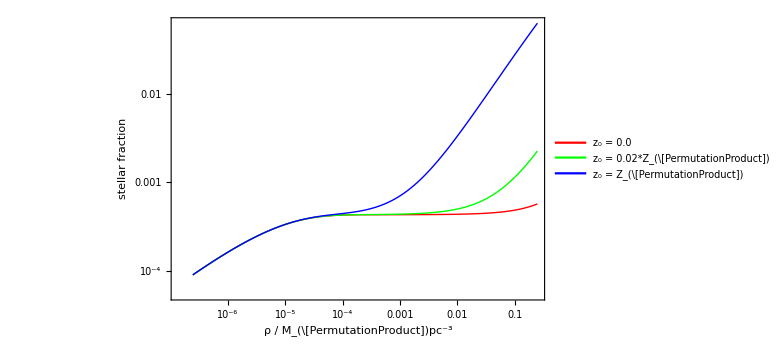

```mathematica
ListLogLogPlot[
data,
Joined->True,
PlotStyle->{{Thick,Red},{Thick,Green},{Thick,Blue}},
PlotTheme->"Detailed",
PlotLegends->Placed[{"z_0 = 0.0", "z_0 = 0.02*Z_(\[PermutationProduct])","z_0 = Z_(\[PermutationProduct])"},{Left,Top}],
PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},
FrameStyle->Directive[Black,14],
FrameLabel->{Style["ρ / M_(\[PermutationProduct])pc^-3",16],Style["stellar fraction",16] },
ImageSize->Large
]
```